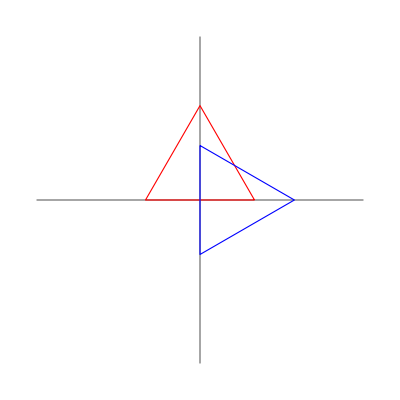

```mathematica
With[{transform={{0,1},{1,0}},
points={{1,0},{0,Sqrt[3]},{-1,0}},
axes=3},
Show[
Graphics[{Gray,Line[{{0,-axes},{0,axes}}]}],
Graphics[{Gray,Line[{{-axes,0},{axes,0}}]}],
Graphics[{EdgeForm[{Red, Thick}],FaceForm[Transparent],Polygon[points]}],
Graphics[{EdgeForm[{Blue,Thick}],FaceForm[Transparent],Polygon[points.Transpose[transform]]}]
]
]
```

```mathematica
DrawTransform[transform_]:=With[{
points={{1,1},{0,Sqrt[3]+1},{-1,1}},
axes=4},
Print[points];
Print[points.transform];
Print[points.Transpose[transform]];
Show[
Graphics[{Gray,Line[{{0,-axes},{0,axes}}]}],
Graphics[{Gray,Line[{{-axes,0},{axes,0}}]}],
Graphics[{EdgeForm[{Darker[Green]}],FaceForm[Transparent],Polygon[points]}],
Graphics[{EdgeForm[{Dotted,Red, Thick}],FaceForm[Transparent],Polygon[points.transform]}],
Graphics[{EdgeForm[{Dashed,Blue}],FaceForm[Transparent],Polygon[points.Transpose[transform]]}]
]
]
```

```mathematica
{1,1}.{{1,1},{1,0}}
```

{2,1}

{{1,1},{0,1+√3},{-1,1}}

{{1,1},{1+√3,0},{1,-1}}

{{1,1},{1+√3,0},{1,-1}}

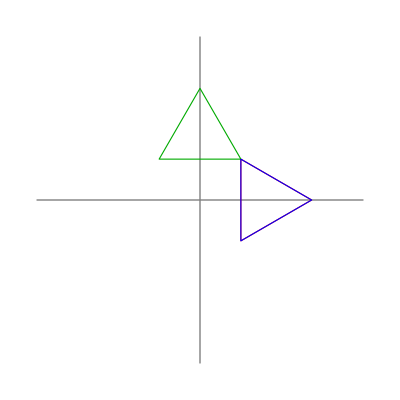

```mathematica
DrawTransform[{{0,1},{1,0}}]
```

{{1,1},{0,1+√3},{-1,1}}

{{1,1},{0,1+√3},{-1,1}}

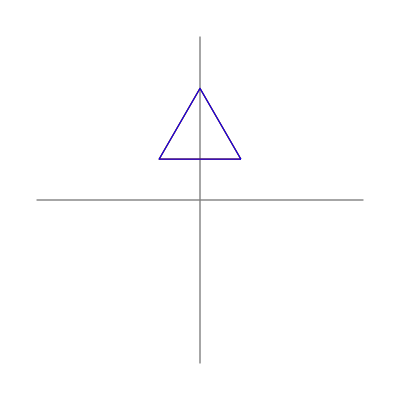

```mathematica
DrawTransform[{{1,0},{0,1}}]
```

{{1,1},{0,1+√3},{-1,1}}

{{2,-1},{1+√3,0},{0,1}}

{{0,1},{-1-√3,0},{-2,-1}}

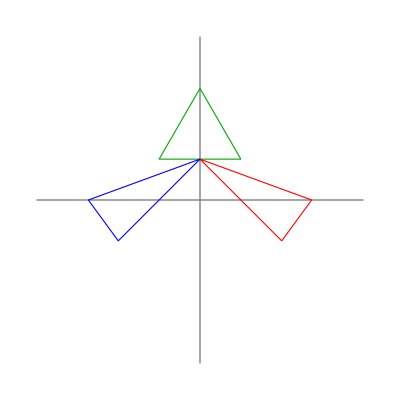

```mathematica
DrawTransform[{{1,-1},{1,0}}]
```

{{1,1},{0,1+√3},{-1,1}}

{{2,-1+√2},{1+√3,√2 (1+√3)},{0,1+√2}}

{{0,1+√2},{-1-√3,√2 (1+√3)},{-2,-1+√2}}

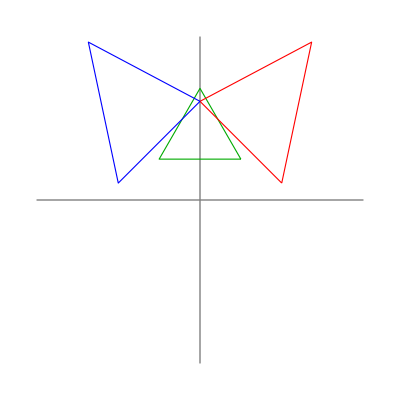

```mathematica
DrawTransform[{{1,-1},{1,Sqrt[2]}}]
```

```mathematica
With[{transform={{0,1},{1,0}},
points={{1,0},{0,Sqrt[3]},{-1,0}}},
Transpose[transform]
]
```

{{0,1},{1,0}}

```mathematica
With[{transform={{0,1},{1,0}},
points={{1,0},{0,Sqrt[3]},{-1,0}}},
points.Transpose[transform]
]
```

{{0,1},{√3,0},{0,-1}}

{{1,1},{0,1+√3},{-1,1}}

{{2,1},{1+√3,0},{0,-1}}

{{2,1},{1+√3,0},{0,-1}}

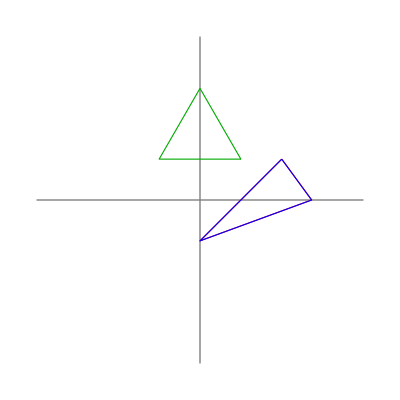

```mathematica
DrawTransform[{{1,1},{1,0}}]
```

{{1,1},{0,1+√3},{-1,1}}

{{1,2},{0,1+√3},{-1,0}}

{{2,1},{1+√3,1+√3},{0,1}}

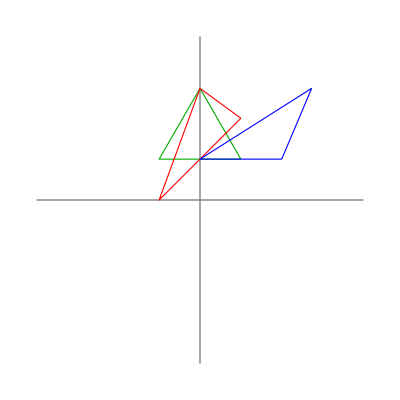

```mathematica
DrawTransform[{{1,1},{0,1}}]
```

```mathematica
With[{transform={{1,0},{1,1}}},
Solve[{x,y}.transform=={x,y}.Transpose[transform],{x,y}]
]
```

{{x→0,y→0}}

```mathematica
Solve[{x,y}.{{1,1},{0,1}}=={x,y}.Transpose[{{1,1},{0,1}}],{x,y}]
```

{{x→0,y→0}}

```mathematica
With[{transform={{1,0},{0,1}}},
Solve[{x,y}.transform=={x,y}.Transpose[transform],{x,y}]
]
```

{{}}

```mathematica
With[{transform={{a,b},{c,d}}},
Reduce[{x,y}.transform=={x,y}.Transpose[transform],{x,y}]
]
```

(x==0&&y==0)||b==c

```mathematica
With[{size=2},
With[{transform=Table[Indexed[a,{i,j}],{i,size},{j,size}], vector=Table[Indexed[x,i],{i,size}]},
BooleanMinimize[Reduce[vector.transform==vector.Transpose[transform],vector],"DNF"]
]
]
```

a12==a21||(x1==0&&x2==0)

```mathematica
Table[With[{size=k},
With[{transform=Table[Indexed[a,{i,j}],{i,size},{j,size}], vector=Table[Indexed[x,i],{i,size}]},
Reduce[vector.transform==vector.Transpose[transform],vector]
]
]//Length,{k,1,4}]
```

{0,2,5,11}

```mathematica
With[{transform={{a,b},{c,d}}},
Reduce[{x,y}.transform=={x,y}.Transpose[transform]]
]
```

(y==0&&x==0)||b==c

```mathematica
With[{size=3},
Table[Indexed[a,{i,j}]==0,{i,size-1},{j,i}]
]
```

{{a11==0},{a21==0,a22==0}}

```mathematica
With[{exp=With[{size=4},
With[{transform=Table[Indexed[a,{i,j}],{i,size},{j,size}], vector=Table[Indexed[x,i],{i,size}]},
BooleanMinimize[Map[Factor,Reduce[vector.transform==vector.Transpose[transform],vector]
&&Fold[And,Map[#≠0&,vector]]
&&Fold[And,Table[Indexed[a,{i,i}]==1,{i,size}]]
&&Table[Indexed[a,{i,j}]==0,{i,size-1},{j,i}]
],"CNF"]
]
]},
Table[exp[[i]],{i,Length[exp]}]]//Sort//TableForm
```

a11==1 |  | 
a22==1 |  | 
a33==1 |  | 
a44==1 |  | 
a11==0 | a21==0
a22==0 | a31==0
a32==0
a33==0
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a34==a43 |  | 
a34==a43||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a34==a43||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a34==a43||-a34+a43≠0 |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a14==a41 |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a24==a42 |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a14==a41||x2==-((a14-a41) x1)/(a24-a42) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a14==a41||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a14==a41||-a14+a41≠0 |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a14==a41||-a24+a42≠0 |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a24==a42||x2==-((a14-a41) x1)/(a24-a42) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a24==a42||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a24==a42||-a14+a41≠0 |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a24==a42||-a24+a42≠0 |  | 
a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a14==a41||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a14==a41||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a14==a41||-a34+a43≠0 |  | 
a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a24==a42||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a24==a42||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a24==a42||-a34+a43≠0 |  | 
a14==a41||x2==-((a14-a41) x1)/(a24-a42)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a14==a41||x2==-((a14-a41) x1)/(a24-a42)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a14==a41||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a14==a41||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a14==a41||-a14+a41≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a14==a41||-a14+a41≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a14==a41||-a14+a41≠0||-a34+a43≠0 |  | 
a14==a41||-a24+a42≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a14==a41||-a24+a42≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a14==a41||-a24+a42≠0||-a34+a43≠0 |  | 
a14==a41||-a34+a43≠0||x2==-((a14-a41) x1)/(a24-a42) |  | 
a14==a41||-a34+a43≠0||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a24==a42||x2==-((a14-a41) x1)/(a24-a42)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a24==a42||x2==-((a14-a41) x1)/(a24-a42)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a24==a42||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a24==a42||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a24==a42||-a14+a41≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a24==a42||-a14+a41≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a24==a42||-a14+a41≠0||-a34+a43≠0 |  | 
a24==a42||-a24+a42≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a24==a42||-a24+a42≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a24==a42||-a24+a42≠0||-a34+a43≠0 |  | 
a24==a42||-a34+a43≠0||x2==-((a14-a41) x1)/(a24-a42) |  | 
a24==a42||-a34+a43≠0||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==a21||a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||x2==-((a13-a31) x1)/(a23-a32) |  | 
a12==a21||a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||x3==-((a12-a21) x2)/(a13-a31) |  | 
a12==a21||a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||-a13+a31≠0 |  | 
a12==a21||a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||-a23+a32≠0 |  | 
a12==a21||a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||x2==-((a13-a31) x1)/(a23-a32)||x2==-((a14-a41) x1)/(a24-a42) |  | 
a12==a21||a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||x2==-((a13-a31) x1)/(a23-a32)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==a21||a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||x2==-((a14-a41) x1)/(a24-a42)||x3==-((a12-a21) x2)/(a13-a31) |  | 
a12==a21||a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||x3==-((a12-a21) x2)/(a13-a31)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==a21||a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||-a13+a31≠0||x2==-((a14-a41) x1)/(a24-a42) |  | 
a12==a21||a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||-a13+a31≠0||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==a21||a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||-a13+a31≠0||-a14+a41≠0 |  | 
a12==a21||a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||-a13+a31≠0||-a24+a42≠0 |  | 
a12==a21||a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||-a23+a32≠0||x2==-((a14-a41) x1)/(a24-a42) |  | 
a12==a21||a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||-a23+a32≠0||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==a21||a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||-a23+a32≠0||-a14+a41≠0 |  | 
a12==a21||a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||-a23+a32≠0||-a24+a42≠0 |  | 
a12==a21||a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||-a14+a41≠0||x2==-((a13-a31) x1)/(a23-a32) |  | 
a12==a21||a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||-a14+a41≠0||x3==-((a12-a21) x2)/(a13-a31) |  | 
a12==a21||a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||-a24+a42≠0||x2==-((a13-a31) x1)/(a23-a32) |  | 
a12==a21||a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||-a24+a42≠0||x3==-((a12-a21) x2)/(a13-a31) |  | 
a12==a21||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||x2==-((a13-a31) x1)/(a23-a32)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a12==a21||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||x2==-((a13-a31) x1)/(a23-a32)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a12==a21||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||x3==-((a12-a21) x2)/(a13-a31)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a12==a21||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||x3==-((a12-a21) x2)/(a13-a31)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a12==a21||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||-a13+a31≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a12==a21||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||-a13+a31≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a12==a21||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||-a13+a31≠0||-a34+a43≠0 |  | 
a12==a21||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||-a23+a32≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a12==a21||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||-a23+a32≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a12==a21||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||-a23+a32≠0||-a34+a43≠0 |  | 
a12==a21||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||-a34+a43≠0||x2==-((a13-a31) x1)/(a23-a32) |  | 
a12==a21||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||-a34+a43≠0||x3==-((a12-a21) x2)/(a13-a31) |  | 
a12==a21||x2==-((a13-a31) x1)/(a23-a32)||x2==-((a14-a41) x1)/(a24-a42)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a12==a21||x2==-((a13-a31) x1)/(a23-a32)||x2==-((a14-a41) x1)/(a24-a42)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a12==a21||x2==-((a13-a31) x1)/(a23-a32)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==a21||x2==-((a13-a31) x1)/(a23-a32)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==a21||x2==-((a14-a41) x1)/(a24-a42)||x3==-((a12-a21) x2)/(a13-a31)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a12==a21||x2==-((a14-a41) x1)/(a24-a42)||x3==-((a12-a21) x2)/(a13-a31)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a12==a21||x3==-((a12-a21) x2)/(a13-a31)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==a21||x3==-((a12-a21) x2)/(a13-a31)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==a21||-a13+a31≠0||x2==-((a14-a41) x1)/(a24-a42)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a12==a21||-a13+a31≠0||x2==-((a14-a41) x1)/(a24-a42)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a12==a21||-a13+a31≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==a21||-a13+a31≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==a21||-a13+a31≠0||-a14+a41≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a12==a21||-a13+a31≠0||-a14+a41≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a12==a21||-a13+a31≠0||-a14+a41≠0||-a34+a43≠0 |  | 
a12==a21||-a13+a31≠0||-a24+a42≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a12==a21||-a13+a31≠0||-a24+a42≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a12==a21||-a13+a31≠0||-a24+a42≠0||-a34+a43≠0 |  | 
a12==a21||-a13+a31≠0||-a34+a43≠0||x2==-((a14-a41) x1)/(a24-a42) |  | 
a12==a21||-a13+a31≠0||-a34+a43≠0||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==a21||-a23+a32≠0||x2==-((a14-a41) x1)/(a24-a42)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a12==a21||-a23+a32≠0||x2==-((a14-a41) x1)/(a24-a42)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a12==a21||-a23+a32≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==a21||-a23+a32≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==a21||-a23+a32≠0||-a14+a41≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a12==a21||-a23+a32≠0||-a14+a41≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a12==a21||-a23+a32≠0||-a14+a41≠0||-a34+a43≠0 |  | 
a12==a21||-a23+a32≠0||-a24+a42≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a12==a21||-a23+a32≠0||-a24+a42≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a12==a21||-a23+a32≠0||-a24+a42≠0||-a34+a43≠0 |  | 
a12==a21||-a23+a32≠0||-a34+a43≠0||x2==-((a14-a41) x1)/(a24-a42) |  | 
a12==a21||-a23+a32≠0||-a34+a43≠0||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==a21||-a14+a41≠0||x2==-((a13-a31) x1)/(a23-a32)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a12==a21||-a14+a41≠0||x2==-((a13-a31) x1)/(a23-a32)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a12==a21||-a14+a41≠0||x3==-((a12-a21) x2)/(a13-a31)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a12==a21||-a14+a41≠0||x3==-((a12-a21) x2)/(a13-a31)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a12==a21||-a14+a41≠0||-a34+a43≠0||x2==-((a13-a31) x1)/(a23-a32) |  | 
a12==a21||-a14+a41≠0||-a34+a43≠0||x3==-((a12-a21) x2)/(a13-a31) |  | 
a12==a21||-a24+a42≠0||x2==-((a13-a31) x1)/(a23-a32)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a12==a21||-a24+a42≠0||x2==-((a13-a31) x1)/(a23-a32)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a12==a21||-a24+a42≠0||x3==-((a12-a21) x2)/(a13-a31)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a12==a21||-a24+a42≠0||x3==-((a12-a21) x2)/(a13-a31)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a12==a21||-a24+a42≠0||-a34+a43≠0||x2==-((a13-a31) x1)/(a23-a32) |  | 
a12==a21||-a24+a42≠0||-a34+a43≠0||x3==-((a12-a21) x2)/(a13-a31) |  | 
a12==a21||-a34+a43≠0||x2==-((a13-a31) x1)/(a23-a32)||x2==-((a14-a41) x1)/(a24-a42) |  | 
a12==a21||-a34+a43≠0||x2==-((a13-a31) x1)/(a23-a32)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==a21||-a34+a43≠0||x2==-((a14-a41) x1)/(a24-a42)||x3==-((a12-a21) x2)/(a13-a31) |  | 
a12==a21||-a34+a43≠0||x3==-((a12-a21) x2)/(a13-a31)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==a31||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||x2==-((a13-a31) x1)/(a23-a32) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==a31||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||x3==-((a12-a21) x2)/(a13-a31) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==a31||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||-a13+a31≠0 |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==a31||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||-a23+a32≠0 |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==a31||x2==-((a13-a31) x1)/(a23-a32)||x2==-((a14-a41) x1)/(a24-a42) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==a31||x2==-((a13-a31) x1)/(a23-a32)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==a31||x2==-((a14-a41) x1)/(a24-a42)||x3==-((a12-a21) x2)/(a13-a31) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==a31||x3==-((a12-a21) x2)/(a13-a31)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==a31||-a13+a31≠0||x2==-((a14-a41) x1)/(a24-a42) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==a31||-a13+a31≠0||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==a31||-a13+a31≠0||-a14+a41≠0 |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==a31||-a13+a31≠0||-a24+a42≠0 |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==a31||-a23+a32≠0||x2==-((a14-a41) x1)/(a24-a42) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==a31||-a23+a32≠0||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==a31||-a23+a32≠0||-a14+a41≠0 |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==a31||-a23+a32≠0||-a24+a42≠0 |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==a31||-a14+a41≠0||x2==-((a13-a31) x1)/(a23-a32) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==a31||-a14+a41≠0||x3==-((a12-a21) x2)/(a13-a31) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==a31||-a24+a42≠0||x2==-((a13-a31) x1)/(a23-a32) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==a31||-a24+a42≠0||x3==-((a12-a21) x2)/(a13-a31) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a23==a32||x2==-((a13-a31) x1)/(a23-a32) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a23==a32||x3==-((a12-a21) x2)/(a13-a31) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a23==a32||-a13+a31≠0 |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a23==a32||-a23+a32≠0 |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a23==a32||x2==-((a13-a31) x1)/(a23-a32)||x2==-((a14-a41) x1)/(a24-a42) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a23==a32||x2==-((a13-a31) x1)/(a23-a32)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a23==a32||x2==-((a14-a41) x1)/(a24-a42)||x3==-((a12-a21) x2)/(a13-a31) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a23==a32||x3==-((a12-a21) x2)/(a13-a31)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a23==a32||-a13+a31≠0||x2==-((a14-a41) x1)/(a24-a42) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a23==a32||-a13+a31≠0||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a23==a32||-a13+a31≠0||-a14+a41≠0 |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a23==a32||-a13+a31≠0||-a24+a42≠0 |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a23==a32||-a23+a32≠0||x2==-((a14-a41) x1)/(a24-a42) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a23==a32||-a23+a32≠0||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a23==a32||-a23+a32≠0||-a14+a41≠0 |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a23==a32||-a23+a32≠0||-a24+a42≠0 |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a23==a32||-a14+a41≠0||x2==-((a13-a31) x1)/(a23-a32) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a23==a32||-a14+a41≠0||x3==-((a12-a21) x2)/(a13-a31) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a23==a32||-a24+a42≠0||x2==-((a13-a31) x1)/(a23-a32) |  | 
a12==(-a14 a23+a13 a24-a24 a31+a14 a32+a21 a34+a23 a41-a32 a41-a13 a42+a31 a42-a21 a43)/(a34-a43)||a23==a32||-a24+a42≠0||x3==-((a12-a21) x2)/(a13-a31) |  | 
a13==a31||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||x2==-((a13-a31) x1)/(a23-a32)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a13==a31||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||x2==-((a13-a31) x1)/(a23-a32)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a13==a31||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||x3==-((a12-a21) x2)/(a13-a31)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a13==a31||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||x3==-((a12-a21) x2)/(a13-a31)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a13==a31||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||-a13+a31≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a13==a31||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||-a13+a31≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a13==a31||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||-a13+a31≠0||-a34+a43≠0 |  | 
a13==a31||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||-a23+a32≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a13==a31||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||-a23+a32≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a13==a31||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||-a23+a32≠0||-a34+a43≠0 |  | 
a13==a31||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||-a34+a43≠0||x2==-((a13-a31) x1)/(a23-a32) |  | 
a13==a31||a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||-a34+a43≠0||x3==-((a12-a21) x2)/(a13-a31) |  | 
a13==a31||x2==-((a13-a31) x1)/(a23-a32)||x2==-((a14-a41) x1)/(a24-a42)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a13==a31||x2==-((a13-a31) x1)/(a23-a32)||x2==-((a14-a41) x1)/(a24-a42)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a13==a31||x2==-((a13-a31) x1)/(a23-a32)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a13==a31||x2==-((a13-a31) x1)/(a23-a32)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a13==a31||x2==-((a14-a41) x1)/(a24-a42)||x3==-((a12-a21) x2)/(a13-a31)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a13==a31||x2==-((a14-a41) x1)/(a24-a42)||x3==-((a12-a21) x2)/(a13-a31)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a13==a31||x3==-((a12-a21) x2)/(a13-a31)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a13==a31||x3==-((a12-a21) x2)/(a13-a31)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a13==a31||-a13+a31≠0||x2==-((a14-a41) x1)/(a24-a42)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a13==a31||-a13+a31≠0||x2==-((a14-a41) x1)/(a24-a42)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a13==a31||-a13+a31≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a13==a31||-a13+a31≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a13==a31||-a13+a31≠0||-a14+a41≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a13==a31||-a13+a31≠0||-a14+a41≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a13==a31||-a13+a31≠0||-a14+a41≠0||-a34+a43≠0 |  | 
a13==a31||-a13+a31≠0||-a24+a42≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a13==a31||-a13+a31≠0||-a24+a42≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a13==a31||-a13+a31≠0||-a24+a42≠0||-a34+a43≠0 |  | 
a13==a31||-a13+a31≠0||-a34+a43≠0||x2==-((a14-a41) x1)/(a24-a42) |  | 
a13==a31||-a13+a31≠0||-a34+a43≠0||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a13==a31||-a23+a32≠0||x2==-((a14-a41) x1)/(a24-a42)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a13==a31||-a23+a32≠0||x2==-((a14-a41) x1)/(a24-a42)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a13==a31||-a23+a32≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a13==a31||-a23+a32≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a13==a31||-a23+a32≠0||-a14+a41≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a13==a31||-a23+a32≠0||-a14+a41≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a13==a31||-a23+a32≠0||-a14+a41≠0||-a34+a43≠0 |  | 
a13==a31||-a23+a32≠0||-a24+a42≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a13==a31||-a23+a32≠0||-a24+a42≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a13==a31||-a23+a32≠0||-a24+a42≠0||-a34+a43≠0 |  | 
a13==a31||-a23+a32≠0||-a34+a43≠0||x2==-((a14-a41) x1)/(a24-a42) |  | 
a13==a31||-a23+a32≠0||-a34+a43≠0||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a13==a31||-a14+a41≠0||x2==-((a13-a31) x1)/(a23-a32)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a13==a31||-a14+a41≠0||x2==-((a13-a31) x1)/(a23-a32)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a13==a31||-a14+a41≠0||x3==-((a12-a21) x2)/(a13-a31)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a13==a31||-a14+a41≠0||x3==-((a12-a21) x2)/(a13-a31)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a13==a31||-a14+a41≠0||-a34+a43≠0||x2==-((a13-a31) x1)/(a23-a32) |  | 
a13==a31||-a14+a41≠0||-a34+a43≠0||x3==-((a12-a21) x2)/(a13-a31) |  | 
a13==a31||-a24+a42≠0||x2==-((a13-a31) x1)/(a23-a32)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a13==a31||-a24+a42≠0||x2==-((a13-a31) x1)/(a23-a32)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a13==a31||-a24+a42≠0||x3==-((a12-a21) x2)/(a13-a31)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a13==a31||-a24+a42≠0||x3==-((a12-a21) x2)/(a13-a31)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a13==a31||-a24+a42≠0||-a34+a43≠0||x2==-((a13-a31) x1)/(a23-a32) |  | 
a13==a31||-a24+a42≠0||-a34+a43≠0||x3==-((a12-a21) x2)/(a13-a31) |  | 
a13==a31||-a34+a43≠0||x2==-((a13-a31) x1)/(a23-a32)||x2==-((a14-a41) x1)/(a24-a42) |  | 
a13==a31||-a34+a43≠0||x2==-((a13-a31) x1)/(a23-a32)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a13==a31||-a34+a43≠0||x2==-((a14-a41) x1)/(a24-a42)||x3==-((a12-a21) x2)/(a13-a31) |  | 
a13==a31||-a34+a43≠0||x3==-((a12-a21) x2)/(a13-a31)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a23==a32||x2==-((a13-a31) x1)/(a23-a32)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a23==a32||x2==-((a13-a31) x1)/(a23-a32)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a23==a32||x3==-((a12-a21) x2)/(a13-a31)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a23==a32||x3==-((a12-a21) x2)/(a13-a31)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a23==a32||-a13+a31≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a23==a32||-a13+a31≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a23==a32||-a13+a31≠0||-a34+a43≠0 |  | 
a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a23==a32||-a23+a32≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a23==a32||-a23+a32≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a23==a32||-a23+a32≠0||-a34+a43≠0 |  | 
a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a23==a32||-a34+a43≠0||x2==-((a13-a31) x1)/(a23-a32) |  | 
a13==(a14 a23+a24 a31-a14 a32-a23 a41+a32 a41-a31 a42)/(a24-a42)||a23==a32||-a34+a43≠0||x3==-((a12-a21) x2)/(a13-a31) |  | 
a23==a32||x2==-((a13-a31) x1)/(a23-a32)||x2==-((a14-a41) x1)/(a24-a42)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a23==a32||x2==-((a13-a31) x1)/(a23-a32)||x2==-((a14-a41) x1)/(a24-a42)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a23==a32||x2==-((a13-a31) x1)/(a23-a32)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a23==a32||x2==-((a13-a31) x1)/(a23-a32)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a23==a32||x2==-((a14-a41) x1)/(a24-a42)||x3==-((a12-a21) x2)/(a13-a31)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a23==a32||x2==-((a14-a41) x1)/(a24-a42)||x3==-((a12-a21) x2)/(a13-a31)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a23==a32||x3==-((a12-a21) x2)/(a13-a31)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a23==a32||x3==-((a12-a21) x2)/(a13-a31)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a23==a32||-a13+a31≠0||x2==-((a14-a41) x1)/(a24-a42)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a23==a32||-a13+a31≠0||x2==-((a14-a41) x1)/(a24-a42)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a23==a32||-a13+a31≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a23==a32||-a13+a31≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a23==a32||-a13+a31≠0||-a14+a41≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a23==a32||-a13+a31≠0||-a14+a41≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a23==a32||-a13+a31≠0||-a14+a41≠0||-a34+a43≠0 |  | 
a23==a32||-a13+a31≠0||-a24+a42≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a23==a32||-a13+a31≠0||-a24+a42≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a23==a32||-a13+a31≠0||-a24+a42≠0||-a34+a43≠0 |  | 
a23==a32||-a13+a31≠0||-a34+a43≠0||x2==-((a14-a41) x1)/(a24-a42) |  | 
a23==a32||-a13+a31≠0||-a34+a43≠0||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a23==a32||-a23+a32≠0||x2==-((a14-a41) x1)/(a24-a42)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a23==a32||-a23+a32≠0||x2==-((a14-a41) x1)/(a24-a42)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a23==a32||-a23+a32≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a23==a32||-a23+a32≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a23==a32||-a23+a32≠0||-a14+a41≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a23==a32||-a23+a32≠0||-a14+a41≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a23==a32||-a23+a32≠0||-a14+a41≠0||-a34+a43≠0 |  | 
a23==a32||-a23+a32≠0||-a24+a42≠0||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a23==a32||-a23+a32≠0||-a24+a42≠0||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a23==a32||-a23+a32≠0||-a24+a42≠0||-a34+a43≠0 |  | 
a23==a32||-a23+a32≠0||-a34+a43≠0||x2==-((a14-a41) x1)/(a24-a42) |  | 
a23==a32||-a23+a32≠0||-a34+a43≠0||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a23==a32||-a14+a41≠0||x2==-((a13-a31) x1)/(a23-a32)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a23==a32||-a14+a41≠0||x2==-((a13-a31) x1)/(a23-a32)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a23==a32||-a14+a41≠0||x3==-((a12-a21) x2)/(a13-a31)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a23==a32||-a14+a41≠0||x3==-((a12-a21) x2)/(a13-a31)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a23==a32||-a14+a41≠0||-a34+a43≠0||x2==-((a13-a31) x1)/(a23-a32) |  | 
a23==a32||-a14+a41≠0||-a34+a43≠0||x3==-((a12-a21) x2)/(a13-a31) |  | 
a23==a32||-a24+a42≠0||x2==-((a13-a31) x1)/(a23-a32)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a23==a32||-a24+a42≠0||x2==-((a13-a31) x1)/(a23-a32)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a23==a32||-a24+a42≠0||x3==-((a12-a21) x2)/(a13-a31)||x3==-(a14 x1-a41 x1+a24 x2-a42 x2)/(a34-a43) |  | 
a23==a32||-a24+a42≠0||x3==-((a12-a21) x2)/(a13-a31)||x4==(a13 x1-a31 x1+a23 x2-a32 x2)/(a34-a43) |  | 
a23==a32||-a24+a42≠0||-a34+a43≠0||x2==-((a13-a31) x1)/(a23-a32) |  | 
a23==a32||-a24+a42≠0||-a34+a43≠0||x3==-((a12-a21) x2)/(a13-a31) |  | 
a23==a32||-a34+a43≠0||x2==-((a13-a31) x1)/(a23-a32)||x2==-((a14-a41) x1)/(a24-a42) |  | 
a23==a32||-a34+a43≠0||x2==-((a13-a31) x1)/(a23-a32)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
a23==a32||-a34+a43≠0||x2==-((a14-a41) x1)/(a24-a42)||x3==-((a12-a21) x2)/(a13-a31) |  | 
a23==a32||-a34+a43≠0||x3==-((a12-a21) x2)/(a13-a31)||x4==-(a12 x2-a21 x2+a13 x3-a31 x3)/(a14-a41) |  | 
x1≠0 |  | 
x2≠0 |  | 
x3≠0 |  | 
x4≠0 |  |